## Setup and Initialization

The background code be loaded by the following (so long as “loop_amplitudes.m” is in the same directory as the notebook)

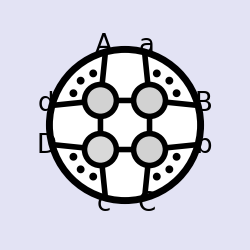
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM

```mathematica
SetDirectory[NotebookDirectory[]];
<<loop_amplitudes.m
```

If the file “loop_amplitudes.m” is copied to your Mathematica’s “Application” directory,

```mathematica
FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

via the command,

```mathematica
If[FileExistsQ[FileNameJoin[{$UserBaseDirectory,"Applications","loop_amplitudes.m"}]],DeleteFile[FileNameJoin[{$UserBaseDirectory,"Applications","loop_amplitudes.m"}]]];CopyFile[FileNameJoin[{NotebookDirectory[],"loop_amplitudes.m"}],FileNameJoin[{$UserBaseDirectory,"Applications","loop_amplitudes.m"}]];
```

then “<<loop_amplitudes.m” can be used in any notebook without any further initialization.

## One-Loop Integrands

### BCFW Recursed Form of One-Loop Integrands

#### Exempli Gratia: The one-loop, 6-particle NMHV amplitude A_6^(1) computed via BCFW recursion

The ℓ-loop, n-point N^(k)MHV amplitude is computed using BCFW recursion by the function “rAmp[n_,k_,ℓ_]”:

```mathematica
egLoopIntegrand=rAmp[6,1,1];
nice@%
```

{R[1,2,3,4,5] K[((23)∩(541)34);((23)∩(541)4(54)∩(321))],R[(451)∩(ℓ),1,2,3,(34)∩((ℓ)1)] K[(134);(145)],R[(23)∩((ℓ)1),3,4,(54)∩((ℓ)1),(451)∩(ℓ)] K[(123);(145)],R[1,3,4,5,6] K[(123);(13(34)∩(651))],R[1,3,4,5,6] K[((34)∩(651)45);((34)∩(651)5(65)∩(431))],R[1,2,3,5,6] K[((23)∩(651)34);((23)∩(651)45)],R[1,2,3,5,6] K[((23)∩(651)45);((23)∩(651)5(65)∩(321))],R[1,2,3,5,6] K[((23)∩(651)34);((23)∩(651)5(65)∩(321))],R[(561)∩(ℓ),1,2,3,4] K[(145);(156)],R[(561)∩(ℓ),2,3,4,(45)∩((ℓ)1)] K[(145);(156)],R[(561)∩(ℓ),1,2,4,(45)∩((ℓ)1)] K[(145);(156)],R[(561)∩(ℓ),1,2,3,(34)∩((ℓ)1)] K[(134);(156)],R[(34)∩((ℓ)1),4,5,(65)∩((ℓ)1),(561)∩(ℓ)] K[(134);(156)],R[(23)∩((ℓ)1),3,4,5,(65)∩((ℓ)1)] K[(123);(156)],R[(23)∩((ℓ)1),4,5,(65)∩((ℓ)1),(561)∩(ℓ)] K[(123);(156)],R[(23)∩((ℓ)1),3,4,(65)∩((ℓ)1),(561)∩(ℓ)] K[(123);(156)]}

This can be converted to a collection of standard superfunctions using the function “fromRform[n_][expression_]” 
which—among other things—converts the symbolic 5-brackets R[a,b,c,d,e] into standard, evaluatable superfunctions.

```mathematica
egAnalyticIntegrand=fromRform[][egLoopIntegrand];
nice@random[%]
```

{(K[(123);(156)])/(⟨34(65)∩((ℓ)1)(561)∩(ℓ)⟩ ⟨4(65)∩((ℓ)1)(561)∩(ℓ)(23)∩((ℓ)1)⟩ ⟨(561)∩(ℓ)(23)∩((ℓ)1)34⟩ ⟨(23)∩((ℓ)1)34(65)∩((ℓ)1)⟩ ⟨(65)∩((ℓ)1)(561)∩(ℓ)(23)∩((ℓ)1)3⟩),(⟨3(ℓ)1⟩ (⟨(ℓ)16⟩ ⟨(ℓ)56⟩ ⟨2345⟩+⟨5(ℓ)1⟩ ⟨(ℓ)56⟩ ⟨2346⟩) | ⟨3(ℓ)1⟩ (⟨(ℓ)16⟩ (⟨(ℓ)56⟩ ⟨3451⟩+⟨1(ℓ)5⟩ ⟨3456⟩)+⟨5(ℓ)1⟩ (⟨(ℓ)56⟩ ⟨3461⟩+⟨61(ℓ)⟩ ⟨3465⟩)) | ⟨3(ℓ)1⟩ (⟨(ℓ)16⟩ (⟨(ℓ)56⟩ ⟨4512⟩+⟨1(ℓ)5⟩ ⟨4562⟩)+⟨5(ℓ)1⟩ (⟨(ℓ)56⟩ ⟨4612⟩+⟨61(ℓ)⟩ ⟨4652⟩)) | ⟨3(ℓ)1⟩ (⟨(ℓ)16⟩ (⟨(ℓ)56⟩ ⟨5123⟩+⟨1(ℓ)5⟩ ⟨5623⟩)+⟨5(ℓ)1⟩ (⟨(ℓ)56⟩ ⟨6123⟩+⟨61(ℓ)⟩ ⟨6523⟩)) | ⟨3(ℓ)1⟩ (⟨5(ℓ)1⟩ ⟨61(ℓ)⟩ ⟨2346⟩+⟨(ℓ)16⟩ (⟨(ℓ)56⟩ ⟨1234⟩+⟨1(ℓ)5⟩ ⟨6234⟩)) | ⟨3(ℓ)1⟩ (⟨1(ℓ)5⟩ ⟨(ℓ)16⟩ ⟨2345⟩+⟨5(ℓ)1⟩ (⟨(ℓ)56⟩ ⟨1234⟩+⟨61(ℓ)⟩ ⟨5234⟩)))}

If f^(k) is a superfunction, it is associated with a pair {f,C} where f is an ordinary function and the matrix C encodes all the component-functions according to

We can evaluate the integrand for a particular component, at a given point in momentum-space by choosing some convenient reference twistors, using for example, the function “exampleTwistors[n_]”

```mathematica
exampleTwistors[6]
```

To see what twistors have been specified, use the function “showTwistors”

```mathematica
showTwistors
```

Z_1 | Z_2 | Z_3 | Z_4 | Z_5 | Z_6
1 | 1 | 1 | 1 | 1 | 1
2 | 3 | 4 | 5 | 6 | 7
3 | 6 | 10 | 15 | 21 | 28
4 | 10 | 20 | 35 | 56 | 84A | B
1 | 1
8 | 9
36 | 45
120 | 165X_1 | X_2
8 | 43
15 | 33
1 | 0
0 | 1

Now we are ready to evaluate the integrand at some point using the function “evaluate[expression_]”:

```mathematica
egNumericIntegrand=evaluate[egAnalyticIntegrand]
```

{{1/60480000,{{1,-4,6,-4,1,0}}},{-1/325337107079577600000000,{{17640,-70560,105840,-70560,17640,0}}},{1/26563124118833351884800000000,{{105840,-423360,635040,-423360,105840,0}}},{-1/70560000000,{{1,0,-10,20,-15,4}}},{1/40320000,{{1,0,-10,20,-15,4}}},{-1/14400000000,{{6,-20,20,0,-10,4}}},{1/134400000,{{6,-20,20,0,-10,4}}},{9/5600000000,{{6,-20,20,0,-10,4}}},{-1/91483862400000,{{301,-1120,1470,-700,-35,84}}},{-1/158459563998489600000,{{126,10080,-41580,63000,-42210,10584}}},{-1/114138423948112058880000,{{42336,-105840,0,211680,-211680,63504}}},{-1/62757929606400000000000,{{42140,-156800,205800,-98000,-4900,11760}}},{1/983819411808642662400000,{{10584,0,-105840,211680,-158760,42336}}},{-1/5893722685196236800000,{{0,11760,-47040,70560,-47040,11760}}},{1/27755321947726464000000000,{{38220,-117600,88200,58800,-102900,35280}}},{1/75560547246105600000000000,{{42140,-156800,205800,-98000,-4900,11760}}}}

A particular component can be extracted using the function  “superComponent[component__][superFunction_].”
For example, the supercomponent proportional to (η_3)^4 would be computed as follows:

```mathematica
egComponentBCFW=superComponent[p,p,m,p,p,p][egNumericIntegrand]
```

-8989/91875

### Chiral Box Expansion of One-Loop Integrands

The chiral box expansion provides an alternative way to represent all loop amplitude integrands in SYM

#### Exempli Gratia: The one-loop, 6-point NMHV amplitude integrand A_6^((1),1) computed via the chiral box expansion

A purely symbolic manifestation of the chiral box expansion is given by “chiralBoxExpansion[n_,k_]”:

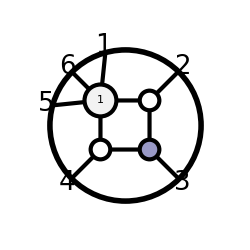
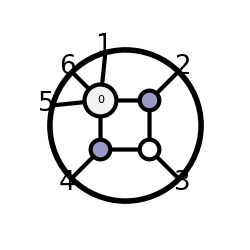
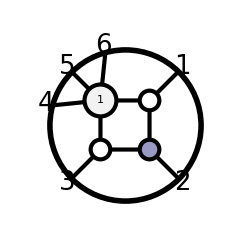
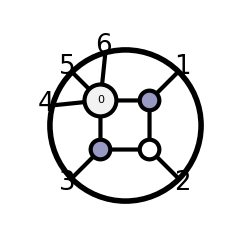
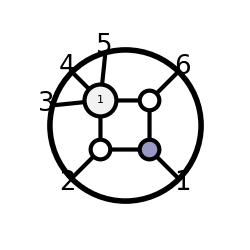
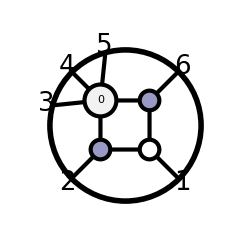
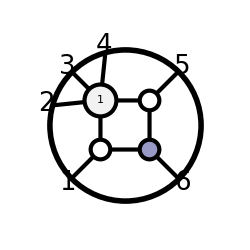
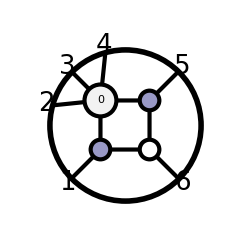
{-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- A_6^(1),-Graphics- A_6^(1),-Graphics- A_6^(1),-Graphics- A_6^(1),-Graphics- A_6^(1),-Graphics- A_6^(1)}

```mathematica
egChiralBoxIntegrand=chiralBoxExpansion[6,1];
nice[%]
```

To make this a bit more intelligible, the cyclic “seeds” which generate the full expansion can be extracted using “onlyCyclicSeeds[expression_]”; and the contributions can be represented graphically using “nice[expression_]”:

```mathematica
egChiralSeeds=onlyCyclicSeeds[egChiralBoxIntegrand]
nice[%]
```

{chiralBox[1][{{2},{3},{4},{5,6,1}}] onShellGraph[1][{{2},{3},{4},{5,6,1}},{-1,0,-1,1}],chiralBox[2][{{2},{3},{4},{5,6,1}}] onShellGraph[2][{{2},{3},{4},{5,6,1}},{0,-1,0,0}],chiralBox[1][{{2},{3},{4,5},{6,1}}] onShellGraph[1][{{2},{3},{4,5},{6,1}},{-1,0,0,0}],chiralBox[2][{{2},{3},{4,5},{6,1}}] onShellGraph[2][{{2},{3},{4,5},{6,1}},{0,-1,0,0}],amp[6,1] scalarBox[{{2},{3},{4,5,6,1}}]}

{-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- -Graphics-,-Graphics- A_6^(1)}

The purely symbolic objects appearing in this expression such as “chiralBox[_][legList_]” can be converted into analytic formulae using “integrand[expression_]”:

```mathematica
nice@integrand[chiralBox[2][{{2},{3},{4,5},{6,1}}]]
```

-(-⟨(X)(123)∩(56(34)∩((ℓ)2))⟩+⟨(X)(356)∩(12(34)∩((ℓ)2))⟩)/(2 ⟨(ℓ)(X)⟩ ⟨(ℓ)12⟩ ⟨(ℓ)23⟩ ⟨(ℓ)34⟩ ⟨(ℓ)56⟩)

The function “analyticIntegrand[expression_]” converts all the symbolic objects—including the all instances of “onShellGraph[_][legList_]” “amp[n_,k_]” etc.—into canonical superfunctions of the form described above:

```mathematica
egAnalyticChiralBoxIntegrand=analyticIntegrand[egChiralBoxIntegrand];
nice[random[%]]
```

{-(⟨(X)61⟩ ⟨5612⟩)/(⟨(ℓ)(X)⟩ ⟨(ℓ)12⟩ ⟨(ℓ)56⟩ ⟨(ℓ)61⟩ ⟨1234⟩ ⟨2345⟩ ⟨3451⟩ ⟨4512⟩ ⟨5123⟩),(⟨2345⟩ | ⟨3451⟩ | ⟨4512⟩ | ⟨5123⟩ | ⟨1234⟩ | 0)}

As before, this set of superfunctions can be evaluated at some point using the function “evaluate[expression_]”:

```mathematica
egNumericChiralBoxIntegrand=evaluate[egAnalyticChiralBoxIntegrand]
```

{{-7111/66108336000000,{{4,-10,0,20,-20,6}}},{-2361/22036112000,{{1,-4,6,-4,1,0}}},{-159/482039950000,{{1,0,-10,20,-15,4}}},{2377/2065885500000,{{4,-15,20,-10,0,1}}},{533/33054168,{{0,1,-4,6,-4,1}}},{111/192815980000,{{6,-20,20,0,-10,4}}},{3001/694137528,{{1,-4,6,-4,1,0}}},{5993/49581252000,{{4,-10,0,20,-20,6}}},{-50027/5666428800000,{{6,-20,20,0,-10,4}}},{-49943/5666428800,{{0,1,-4,6,-4,1}}},{20137/24790626000,{{4,-15,20,-10,0,1}}},{-8429/82635420000,{{1,0,-10,20,-15,4}}},{874/516471375,{{0,1,-4,6,-4,1}}},{117/68862850000,{{6,-20,20,0,-10,4}}},{-22973/30850556800,{{1,-4,6,-4,1,0}}},{12179/13221667200000,{{4,-10,0,20,-20,6}}},{-4657/594975024000,{{4,-10,0,20,-20,6}}},{-116929/14874375600,{{1,-4,6,-4,1,0}}},{99311/247906260000,{{4,-15,20,-10,0,1}}},{-24119/1735343820000,{{1,0,-10,20,-15,4}}},{877/29512650000,{{1,0,-10,20,-15,4}}},{307/82635420000,{{4,-15,20,-10,0,1}}},{-18853/13221667200000,{{6,-20,20,0,-10,4}}},{1788607/13221667200,{{0,1,-4,6,-4,1}}},{-3/482039950,{{1,-4,6,-4,1,0}}},{-3/60254993750,{{1,0,-10,20,-15,4}}},{-3/482039950000,{{6,-20,20,0,-10,4}}},{-789/220361120000,{{1,-4,6,-4,1,0}}},{-789/27545140000000,{{1,0,-10,20,-15,4}}},{-789/220361120000000,{{6,-20,20,0,-10,4}}},{-17819/113328576000,{{1,-4,6,-4,1,0}}},{-17819/14166072000000,{{1,0,-10,20,-15,4}}},{-17819/113328576000000,{{6,-20,20,0,-10,4}}},{-37657/2266571520,{{1,-4,6,-4,1,0}}},{-37657/283321440000,{{1,0,-10,20,-15,4}}},{-37657/2266571520000,{{6,-20,20,0,-10,4}}},{-2210/12395313,{{1,-4,6,-4,1,0}}},{-442/309882825,{{1,0,-10,20,-15,4}}},{-221/1239531300,{{6,-20,20,0,-10,4}}},{-715/49581252,{{1,-4,6,-4,1,0}}},{-143/1239531300,{{1,0,-10,20,-15,4}}},{-143/9916250400,{{6,-20,20,0,-10,4}}}}

And as before, a particular component can be extracted using the function  “superComponent[component__][superFunction_].”
For example, the supercomponent proportional to (η_3)^4 would be computed using:

```mathematica
egChiralBoxComponent=superComponent[p,p,m,p,p,p][egNumericChiralBoxIntegrand]
```

-8989/91875

And we can check that this matches the BCFW-component function:

```mathematica
egComponentBCFW
%==egChiralBoxComponent
```

-8989/91875

True

And we see that the expansion works!

### Comparing the Chiral Box Expansion with BCFW-Recursion

#### Exempli Gratia: the 8-point N^2MHV integrand:

First, we must choose some arbitrary reference momentum-twistors:

```mathematica
exampleTwistors[8]
showTwistors
```

Z_1 | Z_2 | Z_3 | Z_4 | Z_5 | Z_6 | Z_7 | Z_8
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
3 | 6 | 10 | 15 | 21 | 28 | 36 | 45
4 | 10 | 20 | 35 | 56 | 84 | 120 | 165A | B
1 | 1
10 | 11
55 | 66
220 | 286X_1 | X_2
31 | 32
13 | 50
1 | 0
0 | 1

A more compact way to generate the numerically-evaluated BCFW loop integrand is to use the function “nAmp[n_,k_,ℓ_]”:

```mathematica
egBCFWAmp=timed[nAmp[8,2,1]];
```

Evaluation of the function nAmp required , , 756 ms983 μs to complete.

(Notice that we have used the function “timed[expression_]” to time the evaluation process.)

Similarly, a more compact way to generate the numerically-evaluated chiral-box expanded form of the integreand is to use:

```mathematica
egChiralBoxAmp=timed[evaluate[chiralLoopIntegrand[8,2]]];
```

Evaluation of the function evaluate required , , 597 ms666 μs to complete.

Let us compare these two integrands at the specified kinematical point for the component proportional to (η_3)^4(η_5)^4

```mathematica
egBCFWComponent=timed[superComponent[p,m,p,p,m,p,p,p][egBCFWAmp]]
```

Evaluation of the function superComponent[p,m,p,p,m,p,p,p] required , , 18 ms607 μs to complete.

-9504258569159/6223392000000

```mathematica
egChiralBoxComponent=timed[superComponent[p,m,p,p,m,p,p,p][egChiralBoxAmp]]
```

Evaluation of the function superComponent[p,m,p,p,m,p,p,p] required , , 644 ms974 μs to complete.

-9504258569159/6223392000000

```mathematica
egBCFWComponent==egChiralBoxComponent
```

True

#### Exempli Gratia: the 10-point N^3MHV integrand:

First, we must choose some arbitrary reference momentum-twistors:

```mathematica
exampleTwistors[10]
showTwistors
```

Z_1 | Z_2 | Z_3 | Z_4 | Z_5 | Z_6 | Z_7 | Z_8 | Z_9 | Z_10
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66
4 | 10 | 20 | 35 | 56 | 84 | 120 | 165 | 220 | 286A | B
1 | 1
12 | 13
78 | 91
364 | 455X_1 | X_2
4 | 29
50 | 38
1 | 0
0 | 1

A more compact way to generate the numerically-evaluated BCFW loop integrand is to use the function “nAmp[n_,k_,ℓ_]”:

```mathematica
egBCFWAmp=timed[nAmp[10,3,1]];
```

(Notice that we have used the function “timed[expression_]” to time the evaluation process.)

Similarly, a more compact way to generate the numerically-evaluated chiral-box expanded form of the integreand is to use:

```mathematica
egChiralBoxAmp=timed[evaluate[chiralLoopIntegrand[10,3]]];
```

Let us compare these two integrands at the specified kinematical point for the component proportional to (η_1)^4(η_3)^4(η_5)^4

```mathematica
egBCFWComponent=timed[superComponent[m,p,m,p,p,p,p,p,p,m][egBCFWAmp]]
```

```mathematica
egChiralBoxComponent=timed[superComponent[m,p,m,p,p,p,p,p,p,m][egChiralBoxAmp]]
```

```mathematica
egBCFWComponent==egChiralBoxComponent
```

## One-Loop Integrals and Ratio Functions

### Scalar Box Expansion of One-Loop Integrals and Ratio Functions

#### Exempli Gratia: The one-loop, 6-point NMHV amplitude integral A_6^((1),1) computed via the scalar box expansion, with ϵ-regularization

Just like the for the chiral box expansion, the symbolic-level scalar box expansion is generated by “scalarBoxExpansion[n_,k_]”:

```mathematica
egScalarBoxExpansion=scalarBoxExpansion[6,1]
```

And as before, the cyclic-generators of this expansion are extracted using “onlyCyclicSeeds[expression_]”; and the contributions can be represented graphically using “nice[expression_]”:

```mathematica
egScalarSeeds=onlyCyclicSeeds[egScalarBoxExpansion];
nice[%]
```

The purely symbolic objects appearing in this expression such as “scalarBox[legList_]” can be converted into analytic formulae using “integrate[expression_]”:

```mathematica
nice[integrate[egScalarSeeds]]
```

Like the function “analyticIntegrand[expression_]”, the function “analyticIntegral[expression_]” converts all the symbolic objects—including the all instances of “scalarBox[legList_]” “onShellGraph[_][legList_]” “amp[n_,k_]” etc.—into canonical, integrated superfunctions of the form described above:

```mathematica
egScalarBoxIntegral=analyticIntegral[egScalarBoxExpansion];
nice[random[%]]
```

As before, this set of superfunctions can be evaluated at some point using the function “evaluate[expression_]”:

```mathematica
egNumericScalarBoxIntegral=evaluate[egScalarBoxIntegral];
```

And a particular component can be extracted using the function “superComponent[component__][superFunction_]”;
for example, the supercomponent proportional to (η_3)^4 would be computed using:

```mathematica
egScalarBoxComponent=superComponent[p,p,m,p,p,p][egNumericScalarBoxIntegral]
egNumericAmpComponent=N[%,15]
```

We can check that the divergence of this amplitude is equal to the divergence tree-amplitude times the one-loop MHV amplitude

```mathematica
superComponent[p,p,m,p,p,p][evaluate[analyticIntegral[amp[6,1]*scalarBoxExpansion[6,0]]]]
egMHVtimesTree=Expand[N[%,15]]
```

So that we find that the ratio function is then finite:

```mathematica
egRatioFunctionComponentViaScalarBoxes=Chop[Expand[egNumericAmpComponent-egMHVtimesTree]]
```

#### More concise evalutation of the ratio function

As with everything else defined by the “loop_amplitudes” package, there is a more efficient and direct way to evaluate the ratio function—namely, using “ratioIntegral[n_,k_]”; using this, we can check the computation above:

```mathematica
timed[superComponent[p,p,m,p,p,p][evaluate[ratioIntegral[6,1]]]]
N[%,15]
%==egRatioFunctionComponentViaScalarBoxes
```

### Chiral Box Expansion of One-Loop Integrals and Ratio Functions

#### Exempli Gratia: The one-loop, 6-particle NMHV amplitude integral A_6^((1),1) computed via the chiral box expansion, with ϵ-regularization

Just like the for the chiral box expansion, the symbolic-level scalar box expansion is generated by “scalarBoxExpansion[n_,k_]”:

```mathematica
egChiralBoxExpansion=chiralBoxExpansion[6,1]
```

And as before, the cyclic-generators of this expansion are extracted using “onlyCyclicSeeds[expression_]”; and the contributions can be represented graphically using “nice[expression_]”:

```mathematica
egChiralSeeds=onlyCyclicSeeds[egChiralBoxExpansion];
nice[%]
```

The purely symbolic objects appearing in this expression such as “chiralBox[_][legList_]” can be converted into analytic formulae using “integrate[expression_]”:

```mathematica
nice[integrate[egChiralSeeds]]
```

Like the function “analyticIntegrand[expression_]”, the function “analyticIntegral[expression_]” converts all the symbolic objects—including the all instances of “chiralBox[_][legList_]” “onShellGraph[_][legList_]” “amp[n_,k_]” etc.—into canonical, integrated superfunctions of the form described above:

```mathematica
egChiralBoxIntegral=analyticIntegral[egChiralBoxExpansion];
nice[random[%]]
```

As before, this set of superfunctions can be evaluated at some point using the function “evaluate[expression_]”:

```mathematica
egNumericChiralBoxIntegral=evaluate[egChiralBoxIntegral];
```

And a particular component can be extracted using the function “superComponent[component__][superFunction_]”;
for example, the supercomponent proportional to (η_3)^4 would be computed using:

```mathematica
superComponent[p,p,m,p,p,p][egNumericChiralBoxIntegral]
egChiralBoxComponent=Expand[N[%,15]]
```

We can check that the divergence of this amplitude is equal to the divergence tree-amplitude times the one-loop MHV amplitude

```mathematica
superComponent[p,p,m,p,p,p][evaluate[analyticIntegral[amp[6,1]*chiralBoxExpansion[6,0]]]]
egMHVtimesTree=Expand[N[%,15]]
```

So that we find that the ratio function is then finite:

```mathematica
egRatioFunctionComponentViaChiralBoxes=Chop[Expand[egChiralBoxComponent-egMHVtimesTree]]
```

#### Check that the chiral box computation of the ratio function matches the scalar box ratio function

```mathematica
egRatioFunctionComponentViaChiralBoxes==egRatioFunctionComponentViaScalarBoxes
```

#### More concise evalutation of the ratio function

As with everything else defined by the “loop_amplitudes” package, there is a more efficient and direct way to evaluate the ratio function using chiral boxes—namely, using “chiralRatioIntegral[n_,k_]”; using this, we can check the computation above:

```mathematica
timed[superComponent[p,p,m,p,p,p][evaluate[chiralRatioIntegral[6,1]]]]
N[%,15]
%==egRatioFunctionComponentViaScalarBoxes
```

## Evaluation One Loop Ratio Functions

### Exempli Gratia

#### 8-point N^2MHV Ratio Function

Choose random (positive) kinematics:

```mathematica
randomPositiveZs[8]
showTwistors
```

Compute the amplitude using both the scalar boxes and the chiral boxes:

```mathematica
nRatioFunction=timed[evaluate[ratioIntegral[8,2]]];
nRatioFunctionViaChiralBoxes=timed[evaluate[chiralRatioIntegral[8,2]]];
```

Extract the component of the ratio function proportional to (η_1)^4(η_5)^4

```mathematica
timed[superComponent[m,p,p,p,p,m,p,p][N[nRatioFunction,50]]]
timed[superComponent[m,p,p,p,p,m,p,p][N[nRatioFunctionViaChiralBoxes,50]]]
%%==%
```

#### 10-point N^3MHV Ratio Function

Choose random (positive) kinematics:

```mathematica
randomPositiveZs[10]
showTwistors
```

Compute the amplitude using both the scalar boxes and the chiral boxes:

```mathematica
nRatioFunction=timed[evaluate[ratioIntegral[10,3]]];
nRatioFunctionViaChiralBoxes=timed[evaluate[chiralRatioIntegral[10,3]]];
```

Extract the component of the ratio function proportional to (η_1)^4(η_5)^4(η_9)^4

```mathematica
timed[superComponent[m,p,p,m,p,p,p,p,m,p][N[nRatioFunction,50]]]
timed[superComponent[m,p,p,m,p,p,p,p,m,p][N[nRatioFunctionViaChiralBoxes,50]]]
%%==%
```

#### 12-point N^4MHV Ratio Function

Choose random (positive) kinematics:

```mathematica
randomPositiveZs[12]
showTwistors
```

Compute the amplitude using both the scalar boxes and the chiral boxes:

```mathematica
nRatioFunction=timed[evaluate[ratioIntegral[12,4]]];
nRatioFunctionViaChiralBoxes=timed[evaluate[chiralRatioIntegral[12,4]]];
```

Extract the component of the ratio function proportional to (η_1)^4(η_4)^4(η_7)^4(η_10)^4

```mathematica
timed[superComponent[m,p,p,m,p,p,m,p,p,m,p,p][N[nRatioFunction,50]]]
timed[superComponent[m,p,p,m,p,p,m,p,p,m,p,p][N[nRatioFunctionViaChiralBoxes,50]]]
%%==%
```